```mathematica
(* fonction de dispersion des hologrammes en mm et en pixels *)
```

```mathematica
AE=58 (* distance hologramme - CCD en mm *)
```

58

```mathematica
pixel=0.024 (* en mm *)
```

0.024

```mathematica
lambda0=656 (* longueur d'onde connue en nm *)
```

656

```mathematica
AB0pix=600 (* pour cette longueur d'onde, écart à l'ordre 0 en pixels *)
```

600

```mathematica
AB0=AB0pix*0.024 (* en mm *)
```

14.4

```mathematica
g=(1000000)/lambda0*(AB0/AE)/Sqrt[1+(AB0/AE)^2] (* nombre de traits/mm *)
```

367.318

```mathematica
a=1/g (* pas du réseau en mm *)
```

0.00272244

```mathematica
AB[lambda_]:=AE*(lambda/a/1000000)/Sqrt[1-(lambda/a/1000000)^2]/pixel (* pixels en fontion de nm *)
```

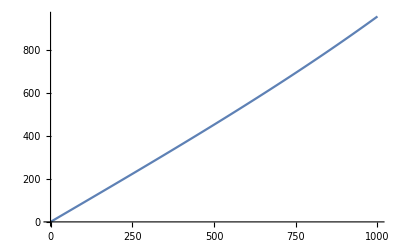

```mathematica
Plot[AB[lambda],{lambda,0,1000}]
```

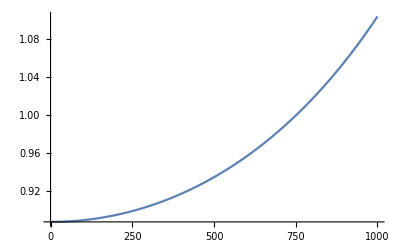

```mathematica
Plot[AB'[lambda],{lambda,0,1000} ](* dérivée -> pixel/nm en fonction de lambda *)
```

```mathematica
(* calcul de la résolution en nm/pixels *)
res= Sin[ArcTan[(pix+e/2)/DD] ]/pas- Sin[ArcTan[(pix-e/2)/DD] ]/pas
```

-(-e/2+pix)/(DD pas √(1+(-e/2+pix)^2/DD^2))+(e/2+pix)/(DD pas √(1+(e/2+pix)^2/DD^2))

```mathematica
Series[res,{e,0,2}]//FullSimplify
```

(DD^3 √(1+pix^2/DD^2) e)/(pas (DD^2+pix^2)^2)+O[e]^3

```mathematica
e*(Tan[i]-Tan[ArcSin[Sin[i]/n]])//FullSimplify
```

e (-Sin[i]/(n √(1-Sin[i]^2/n^2))+Tan[i])

```mathematica
lambda[AB_,theta0_,alpha_,D_,p_,N_]:=(Sin[ArcTan[Tan[theta0+alpha]+AB*pixel/D]-alpha]-Sin[theta0])/(p*N)
```

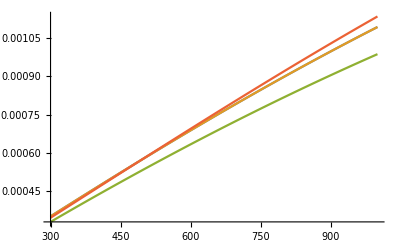

```mathematica
Plot[{lambda[AB,0,0,AE,1,350],lambda[-AB,0,0,AE,-1,350],lambda[AB,0,0.2,AE,1,350],lambda[-AB,0,0.2,AE,-1,350]},{AB,300,1000}]
```

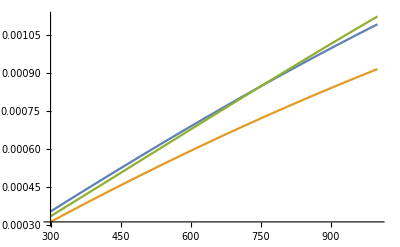

```mathematica
alpha=0.3;
Plot[{lambda[AB,0,0,AE,1,350],lambda[AB,0,alpha,AE,1,350],lambda[-AB,0,alpha,AE,-1,350]},{AB,300,1000}]
```

```mathematica
Distance[AB_,theta0_,alpha_,lambda_,p_,N_]:=AB*pixel/(Tan[ArcSin[p*N*lambda-Sin[theta0]]+alpha]-Tan[theta0+alpha])
```

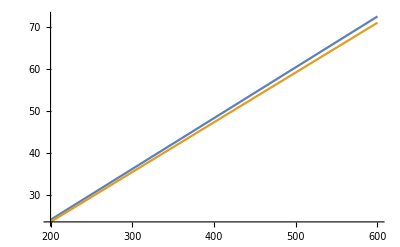

```mathematica
halpha=0.000656;
theta0=0.001; (* radians*)
Plot[{Distance[AB,theta0,0,halpha,1,300],Distance[-AB,theta0,0,halpha,-1,300]},{AB,200,600}]
```

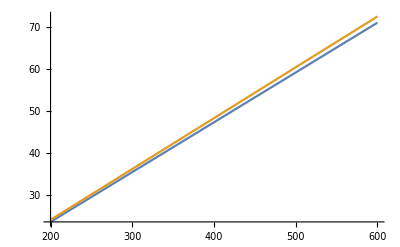

```mathematica
alpha=0.0; (* radians*)
theta0=-0.001; (* radians*)
Plot[{Distance[AB,theta0,alpha,halpha,1,300],Distance[-AB,theta0,alpha,halpha,-1,300]},{AB,200,600}]
```

```mathematica
theta0[x0]:=(x0-IMSIZE/2)*PIXEL2ARCSEC
lambda[x_,x0_,D_]:=(Sin[ArcTan[(x-x0)/D+Tan[theta0[x0]]]]-Sin[theta0[x0]])/(p*NN)
```

```mathematica
D[lambda[x,x0,D],D]//FullSimplify
```

(-x+x0)/(D^2 NN p ((D^2+(x-x0)^2+D Tan[PIXEL2ARCSEC (-IMSIZE/2+x0)] (2 x-2 x0+D Tan[PIXEL2ARCSEC (-IMSIZE/2+x0)]))/D^2)^(3/2))

```mathematica
D[lambda[x,x0,D],x0]//FullSimplify
```

1/(NN p)(-PIXEL2ARCSEC Cos[PIXEL2ARCSEC (-IMSIZE/2+x0)]+(-1+D PIXEL2ARCSEC Sec[PIXEL2ARCSEC (-IMSIZE/2+x0)]^2)/(D ((D^2+(x-x0)^2+D Tan[PIXEL2ARCSEC (-IMSIZE/2+x0)] (2 x-2 x0+D Tan[PIXEL2ARCSEC (-IMSIZE/2+x0)]))/D^2)^(3/2)))